r = 1

```mathematica
UPPERB = 10;
h=0.1;
n=2;
k=0;
α=2+1/2*n;
β=2+1/2*k;
y'[x_,y_,z_]:=Exp[-(y^2+z^2)]+α*x;
z'[x_,y_,z_]:=β*y^2+z;
Subscript[x, 0]=0;
Do[Subscript[x, i]=Subscript[x, i-1]+h,{i,1,UPPERB}];
Subscript[y, 0]=1/2;
Subscript[z, 0]=1;
For[i=0,i≤UPPERB,i++,
Subscript[y, i+1]=Subscript[y, i]+h*y'[Subscript[x, i],Subscript[y, i],Subscript[z, i]];
Subscript[z, i+1]=Subscript[z, i]+h*z'[Subscript[x, i],Subscript[y, i],Subscript[z, i]];
];
```

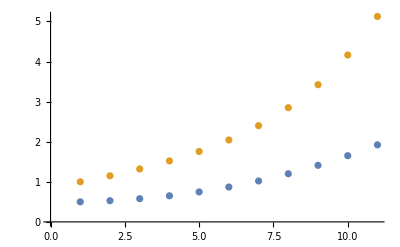

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,UPPERB}],Table[Subscript[z, i],{i,0,UPPERB}]}]
```

```mathematica
Table[Subscript[y, i],{i,0,UPPERB}]
Table[Subscript[z, i],{i,0,UPPERB}]
```

{1/2,0.52865,0.5788,0.651296,0.747789,0.870399,1.02112,1.20123,1.41123,1.65123,1.92123}

{1,1.15,1.32089,1.51999,1.75682,2.04434,2.40029,2.84886,3.42234,4.16289,5.12449}

r = 4

```mathematica
Do[Unset[Subscript[z, i]],{i,1,UPPERB}];
Do[Unset[Subscript[y, i]],{i,1,UPPERB}];
For[i=0,i≤UPPERB,i++,
Subscript[k1, y]=h*y'[Subscript[x, i],Subscript[y, i],Subscript[z, i]];
Subscript[k1, z]=h*z'[Subscript[x, i],Subscript[y, i],Subscript[z, i]];
Subscript[k2, y]=h*y'[Subscript[x, i]+h/2,Subscript[y, i]+Subscript[k1, y]/2,Subscript[z, i]+Subscript[k1, z]/2];
Subscript[k2, z]=h*z'[Subscript[x, i]+h/2,Subscript[y, i]+Subscript[k1, y]/2,Subscript[z, i]+Subscript[k1, z]/2];
Subscript[k3, y]=h*y'[Subscript[x, i]+h/2,Subscript[y, i]+Subscript[k2, y]/2,Subscript[z, i]+Subscript[k2, z]/2];
Subscript[k3, z]=h*z'[Subscript[x, i]+h/2,Subscript[y, i]+Subscript[k2, y]/2,Subscript[z, i]+Subscript[k2, z]/2];
Subscript[k4, y]=h*y'[Subscript[x, i]+h,Subscript[y, i]+Subscript[k3, y],Subscript[z, i]+Subscript[k3, z]];
Subscript[k4, z]=h*z'[Subscript[x, i]+h,Subscript[y, i]+Subscript[k3, y],Subscript[z, i]+Subscript[k3, z]];
Subscript[y, i+1]=Subscript[y, i]+1/6*(Subscript[k1, y]+2*Subscript[k2, y]+2*Subscript[k3, y]+Subscript[k4, y]);
Subscript[z, i+1]=Subscript[z, i]+1/6*(Subscript[k1, z]+2*Subscript[k2, z]+2*Subscript[k3, z]+Subscript[k4, z]);
];
```

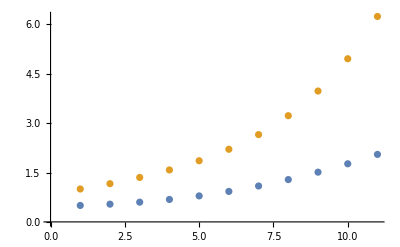

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,UPPERB}], Table[Subscript[z, i],{i,0,UPPERB}]}]
```

```mathematica
Table[Subscript[y, i],{i,0,UPPERB}]
Table[Subscript[z, i],{i,0,UPPERB}]
```

{1/2,0.538985,0.599176,0.682187,0.790418,0.92629,1.09142,1.28643,1.51143,1.76643,2.05143}

{1,1.16152,1.3513,1.57916,1.85852,2.20801,2.65316,3.22813,3.97759,4.95886,6.24439}